# DOD = 1 Triangle subtraction example

## Tooling

```mathematica
SetAttributes[SP4,Orderless];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/UV_derivatives_with_CFF_final/DOD1_example/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

```mathematica
ClearAll[GenerateLMBData];
GenerateLMBData[g_,OptionsPattern[{loopshift->{},externalshift->{}}]]:=Module[
{
edges=EdgeList[g],
props,
shift,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
shift=If[AllTrue[props["sig"]⟦1⟧,(#===0)&],
OptionValue[externalshift]
,
OptionValue[loopshift]
];
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
(
((props["sig"]⟦1⟧.Table[q[i],{i,lmbEdgesIDs}])
+(props["sig"]⟦2⟧.Table[q[(e/.DirectedEdge[_,_,props_]:>props)["id"]],{e,externals}]))/.shift
)
)
|>
,{e,edges}
]]
]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
GetVirtualPropagatorsIDs[g_]:=
Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,GetVirtualPropagators[g]}]
```

```mathematica
ExpandSP4[Num_]:=TensorExpand[Num/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]}
```

```mathematica
NorExactZero[expr_]:=If[Evaluate[FullSimplify[expr]]===0,0,N[expr]]
```

```mathematica
ClearAll[ComputeSubtractionTermFromNormalized];
ComputeSubtractionTermFromNormalized[ct_,numerics_]:=Module[{lmbEdges,orkey,sortedEdgeIDs},
lmbEdges=cFFGetLMBEdges[ct["graph"]];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
(-1)^Length[sortedEdgeIDs]/(-I)^Length[lmbEdges](1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
ClearAll[ComputeSubtractionTerm];
ComputeSubtractionTerm[ct_,numerics_,OptionsPattern[{NumeratorFudge->None, DebugNumerator->False}]]:=Module[
{orkey,sortedEdgeIDs,scalednumerics,ResPerOrientations,OSEReplacement,ShiftsReplacement,lmbEdges,externalEdges,g,orientationsForThisTerm,
signatures,momLabels,reducedGraph,reducedGraphEdgeList,processedNum, numForThisOrientation,internalOSEs,normalization,tmpKey,resForThisOrientation},
g=ct["graph"];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[g]}]];
scalednumerics=numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]};
momLabels=cFFGenerateMomentaLabels[g];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];

lmbEdges=cFFGetLMBEdges[g];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=EdgeList[reducedGraph];
ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}]/.numerics;

processedNum=TensorExpand[ct["num"]/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};processedNum=((((processedNum/.{SP4[a_,b_]:>(a[0]*b[0]-a . b)})/.{q[i_][0]:>qE[i]})/.{q[i_]:>(signatures[i][[1]] . momLabels[[1]]+signatures[i][[2]] . momLabels[[2]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);

If[OptionValue[DebugNumerator],
Print["Numerator:"];
Print[processedNum];
];
If[Not[OptionValue[NumeratorFudge]===None],
processedNum=OptionValue[NumeratorFudge][processedNum];
If[OptionValue[DebugNumerator],
Print["Numerator after fudge:"];
Print[processedNum];
];
];

processedNum=processedNum/.ShiftsReplacement;
processedNum=processedNum/.scalednumerics;


OSEReplacement=If[
Length[scalednumerics]==0,
{},
ComputeOSEReplacements[g,scalednumerics]
];

normalization=( (*(-I)^Length[lmbEdges]*)1/ ((Times@@Table[2*OSE[(e/.{DirectedEdge[_,_,props_]:>props})["id"]],{e,EdgeList[reducedGraph]}])) );

Association[SortBy[Table[
(*
orkey=Table[
If[o,-1,1],
{o,orientation⟦1⟧}
];
*)
orkey=Table[
tmpKey=Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"];
orientation⟦1⟧[tmpKey],
{e,reducedGraphEdgeList}
];

orientationsForThisTerm=Association[Table[
tmpKey=Evaluate[(reducedGraphEdgeList⟦ie⟧/.{DirectedEdge[_,_,props_]:>props})]["id"];
tmpKey->orkey⟦ie⟧,{ie,Length[reducedGraphEdgeList]}]];

numForThisOrientation=processedNum/.Table[qE[edgeID]->(orientationsForThisTerm[edgeID]*OSE[edgeID]),{edgeID,Keys[orientationsForThisTerm]}];

resForThisOrientation=(1/λ)^3((normalization orientation⟦2⟧numForThisOrientation)/.scalednumerics);

If[MemberQ[Keys[ct],"dots"],
Do[
Do[
resForThisOrientation=1/(2OSE[d])D[resForThisOrientation,OSE[d]]
,{id,ct["dots"][d]-1}];
resForThisOrientation=resForThisOrientation/Gamma[ct["dots"][d]]
,{d,Keys[ct["dots"]]}];
];
resForThisOrientation=resForThisOrientation/.OSEReplacement;
orkey->resForThisOrientation
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]
]
```

```mathematica
ConvertCFFFormat[structuredCFF_,g_]:=Module[
{externalEdges,ShiftsReplacement,reducedGraph,flipConfiguration,tmpOrientation,momLabels},
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];

ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}];
momLabels=cFFGenerateMomentaLabels[g];

Table[
flipConfiguration=Association[Table[
tmpOrientation=o["Orientation"][Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"]];
e->tmpOrientation,{e,EdgeList[reducedGraph]}]];
{
o["Orientation"],

Total[Table[
1/Times@@Table[
es["overall_sign"]*(
Total[Table[OSE[ose],{ose,es["OSE"]}]]+
(cFFGenerateEnergyShiftSignatureForEsurf[g,es["OSE"],flipConfiguration].Table[ToExpression[ToString[p]<>"E"],{p,momLabels⟦2⟧}])/.ShiftsReplacement
)
,{es,t["Esurfs"]}
],{t,o["Terms"]}]]
}
,{o,structuredCFF}]
]
```

```mathematica
ClearAll[AnalyzeSubtraction];
AnalyzeSubtraction[Ires_,SubtractionRes_,lambdaTerm_,OptionsPattern[{fudges-><||>,ExpansionDepth->0}]]:=Module[
{tmpI,tmpCTs,sumCTs,res},
(*
fudges=<|
"NumExpansion"->{1},
"NumDOSEDot"->{1,1,1},
"CFFDOSEDot"->{1,1,1}
|>;
*)
res=Table[
tmpI=SeriesCoefficient[Series[Ires[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0],lambdaTerm]/.{Missing[x__]:>0};
tmpCTs=Association[Table[k->Table[
If[MemberQ[Keys[OptionValue["fudges"]],k],OptionValue["fudges"][k]⟦is⟧,1]
*If[
SubtractionRes[k]⟦is⟧[o]===0,
0,
SeriesCoefficient[Series[SubtractionRes[k]⟦is⟧[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0],lambdaTerm]/.{Missing[x__]:>0},
]
,{is,Length[SubtractionRes[k]]}],{k,Keys[SubtractionRes]}]];
sumCTs=FullSimplify[Total[Table[Total[tmpCTs[k]],{k,Keys[tmpCTs]}]]];
Join@@{
{o},
{ NorExactZero[tmpI],NorExactZero[-sumCTs],NorExactZero[tmpI-sumCTs]},
Flatten[Table[NorExactZero[tmpCTs[k]],{k,Keys[tmpCTs]}]]
}
,{o,Keys[Ires]}
];
res=Join[{Join@@{
{"orientation","I","-SumCT","I-SumCT"},
Flatten[Table[Table[k<>"#"<>ToString[ik],{ik,Length[tmpCTs[k]]}],{k,Keys[tmpCTs]}]]
}},res];
AppendTo[res,Join[{"TOTAL"},
Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]
]]
]
```

## Test

### Input

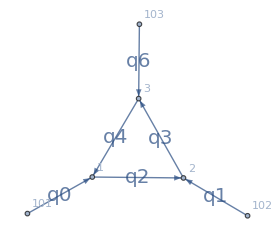

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[1,2,2],
DirectedEdge[2,3,3],
DirectedEdge[3,1,4],
DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|2->1,3->2,4->3|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
lmbVec=q[cFFGetLMBEdges[Tri1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}];
```

```mathematica
Dataset[GenerateLMBData[Tri1L,loopshift->{q[0]:>(-q[1]-q[6])}]]
```

```mathematica
lmbData=GenerateLMBData[Tri1L,loopshift->{q[0]:>(-q[1]-q[6])}];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|0→<|mass→0,lmb_decomposition→λ q[0]|>,1→<|mass→0,lmb_decomposition→λ q[1]|>,2→<|mass→λ,lmb_decomposition→-λ q[1]+q[3]|>,3→<|mass→2 λ,lmb_decomposition→q[3]|>,4→<|mass→3 λ,lmb_decomposition→q[3]+λ q[6]|>,6→<|mass→0,lmb_decomposition→λ q[6]|>|>

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147}

See how some small off-shellness in the external violates the subtraction

```mathematica
(* Tri1Lnumerics=Join[Tri1Lnumerics⟦;;-2⟧,{p3E->Evaluate[(p3E/.Tri1Lnumerics)]+1/3}] *)
```

```mathematica
subtractionNumerics=Join[
Tri1Lnumerics,
{mUV->10,
p[1][0]->(p1E/.Tri1Lnumerics),p[2][0]->(p2E/.Tri1Lnumerics),p[3][0]->(p3E/.Tri1Lnumerics),
p[1]->(p1/.Tri1Lnumerics),p[2]->(p2/.Tri1Lnumerics),p[3]->(p3/.Tri1Lnumerics)
}];
```

```mathematica
UVExternalsDefinition=Block[
{
externalEdges,externalEdgesIDs,momLabels,signatures
},
externalEdges=cFFGetExternalEdges[Tri1L];
externalEdgesIDs=Table[Evaluate[(ee/.{DirectedEdge[_,_,props_]:>props})]["id"],{ee,externalEdges}];
momLabels=cFFGenerateMomentaLabels[Tri1L];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Tri1L]}]];

Join[
(*Table[
q[eeID]->(signatures[eeID][[1]] . momLabels[[1]]+signatures[eeID][[2]] . momLabels[[2]])
,{eeID,externalEdgesIDs}],*)
Table[
q[externalEdgesIDs⟦ieeID⟧]->p[ieeID]
,{ieeID,Length[externalEdgesIDs]}],
Table[
qE[externalEdgesIDs⟦ieeID⟧]->ToExpression["p"<>ToString[ieeID]<>"E"]
,{ieeID,Length[externalEdgesIDs]}]
]
]
```

{q[0]→p[1],q[1]→p[2],q[6]→p[3],qE[0]→p1E,qE[1]→p2E,qE[6]→p3E}

```mathematica
Tri1Lnumerator=-SP4[q[2],q[4]]SP4[q[3],q[6]];
```

```mathematica
SubtractionData=<|
"I"-><|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>
|>;
```

```mathematica
ComputeOSEReplacements[Tri1L,Tri1Lnumerics/.{Rule[k1,a_]->Rule[k1,1/λ a]}]
```

{OSE[0]:>(√10080339)/2431,OSE[1]:>(3 √37688387)/12673,OSE[2]:>√(1+(-19/23+3/(5 λ))^2+(-17/19+2/(3 λ))^2+(-23/29+5/(7 λ))^2),OSE[3]:>√(4+14494/(11025 λ^2)),OSE[4]:>√(9+(-500/299+3/(5 λ))^2+(-320/209+2/(3 λ))^2+(-768/493+5/(7 λ))^2),OSE[6]:>(4 √448907742480209)/30808063}

```mathematica
EdgeList[GraphDifference[Tri1L,DirectedGraph[cFFGetExternalEdges[Tri1L]]]]
```

{12<|id→2,sig→{{1},{0,-1,0}},mass→1|>,23<|id→3,sig→{{1},{0,0,0}},mass→2|>,31<|id→4,sig→{{1},{-1,-1,0}},mass→3|>}

Test the new evaluation model against the old one

```mathematica
Simplify[
ComputeSubtractionTermFromNormalized[
<|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->Tri1Lnumerator,
"graph"->Tri1L,
"dots"-><|2->1|>
|>,
Tri1Lnumerics(*{}*)][{-1,-1,1}]
]
```

0

Consistency check

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
(*Tri1Lnumerics*){}][{-1,-1,1}]
```

1/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
{}][{-1,-1,1}]
```

1/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2),
"graph"->Tri1L,
"dots"-><|4->2|>
|>,
{}][{-1,-1,1}]
```

(1/(4 λ^3 OSE[2] OSE[3] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))-(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4])^2)-(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4])^2 (p1E+p2E+OSE[3]+OSE[4]))-(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4]^2 (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4])))/(2 OSE[4])

```mathematica
Simplify[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2)^3,
"graph"->Tri1L,
"dots"-><|4->4,3->1|>
|>,
Tri1Lnumerics][{-1,-1,1}]
]
```

0

```mathematica
Simplify[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2)^2(SP4[q[3],q[3]]-2^2)^3,
"graph"->Tri1L,
"dots"-><|4->3,3->4|>
|>,
Tri1Lnumerics][{-1,-1,1}]]
```

0

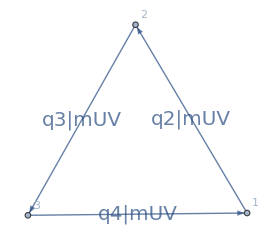

```mathematica
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,2],
DirectedEdge[2,3,3],
DirectedEdge[3,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|2->mUV,3->mUV,4->mUV|>,lmb->{3}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]]
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
SubtractionContribs=<||>;
```

### Numerator decomposition

```mathematica
Tri1L4DExpr=Num[Tri1Lnumerator]/Times@@Table[1/λ^2 Denom[ie,SP4[q[ie][λ],q[ie][λ]]-λ^2 m[ie]^2+(m[ie]^2-mUV^2)],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
```

(λ^6 Num[-SP4[q[2],q[4]] SP4[q[3],q[6]]])/(Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDep=Collect[(1/λ)^4 Tri1L4DExpr/.
{
Num[x__]:>(x
/.
Table[q[ie]->1/λ q[ie][λ],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
/.{
SP4[1/λ a_,1/λ b_]:>1/λ^2 SP4[a,b]
}/.
{SP4[1/λ a_,b_]:>1/λ SP4[a,b]}
)
},λ]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits=Association[Table[pwr->λ^pwr Coefficient[Tri1L4DExprWithFullLambdaDep,λ^pwr],{pwr,{-1,1,2}}]]
```

<|-1→-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]]),1→0,2→0|>

```mathematica
AssociateTo[Tri1L4DExprWithFullLambdaDepDODsplits,0->Tri1L4DExprWithFullLambdaDep-Total[Values[Tri1L4DExprWithFullLambdaDepDODsplits]]];
```

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits
```

<|-1→-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]]),1→0,2→0,0→0|>

### Subtraction of λ^-1 leading UV contribution

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits[-1]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
lm1Numerator=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}(*/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])}*)
```

-SP4[q[2],q[4]] SP4[q[3],q[6]]

```mathematica
AssociateTo[SubtractionContribs,
"λm1CT"->{
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->lm1Numerator,
"graph"->Tri1LUVTopology,
"dots"-><|2->1,3->1,4->1|>
|>
}
];
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"]
|>,subtractionNumerics])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,-1]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1
{-1,-1,1} | 0.214368 | -0.214368 | 0 | 0.214368
{-1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,1} | 0.0457567 | -0.0457567 | 0 | 0.0457567
{1,-1,-1} | 0.214368 | -0.214368 | 0 | 0.214368
{1,-1,1} | 0 | 0 | 0 | 0.
{1,1,-1} | 0.0457567 | -0.0457567 | 0 | 0.0457567
TOTAL | 0.52025 | -0.52025 | 0 | 0.52025)

### Subtraction of λ^0 sub-leading UV contribution

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits[-1]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
dod0Expr=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1]+Tri1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

```mathematica
dod0Expr
```

-(SP4[q[2][0],q[4][0]] q[3]'[0] SP4^(0,1)[q[6],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[2]'[0] Denom^(0,1)[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] SP4^(0,1)[q[2][0],q[2][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]]^2 Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])-(SP4[q[6],q[3][0]] q[4]'[0] SP4^(0,1)[q[2][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[3]'[0] Denom^(0,1)[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] SP4^(0,1)[q[3][0],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]]^2 Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[4]'[0] Denom^(0,1)[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]] SP4^(0,1)[q[4][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]]^2)+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[2]'[0] Denom^(0,1)[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] SP4^(1,0)[q[2][0],q[2][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]]^2 Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])-(SP4[q[6],q[3][0]] q[2]'[0] SP4^(1,0)[q[2][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[3]'[0] Denom^(0,1)[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] SP4^(1,0)[q[3][0],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]]^2 Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[4]'[0] Denom^(0,1)[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]] SP4^(1,0)[q[4][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]]^2)

Now split the above expression into its various denominator structures

```mathematica
Dataset[lmbDataLambda]
```

```mathematica
Tri1Lnumerator
```

-SP4[q[2],q[4]] SP4[q[3],q[6]]

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→SP4[q[1],q[4]] SP4[q[3],q[6]]-SP4[q[2],q[6]] SP4[q[3],q[6]]|>

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDNumNoDot"->{
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->dod0NumNoDot[{}],
"graph"->Tri1LUVTopology,
"dots"-><|2->1,3->1,4->1|>
|>
}
];
```

```mathematica
dod0NumDotted=Association[Table[{{dot}->ExpandSP4[dod0Expr/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_,__]):>0}/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_?(!#1===dot&),__]^2):>0}/.{Denom[y__]:>1}/.x__ q[dot]'[0] Derivative[0,1][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.x__ q[dot]'[0] Derivative[1,0][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.SP4[0,x__]:>0/.{q[ie_][0]->q[ie]}]},{dot,
Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[Tri1L]}]]
}]]
```

<|{2}→-2 SP4[q[1],q[2]] SP4[q[2],q[4]] SP4[q[3],q[6]],{3}→0,{4}→2 SP4[q[2],q[4]] SP4[q[3],q[6]] SP4[q[4],q[6]]|>

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDDenomDotted"->
Table[
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->dod0NumDotted[d],
"graph"->Tri1LUVTopology,
"dots"-><|d⟦1⟧->2|>
|>
,{d,Sort[Keys[dod0NumDotted]]}]
];
```

```mathematica
(*
ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["cFFexpr"],
"graph"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["graph"],
"dots"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["dots"]
|>,subtractionNumerics,
DebugNumerator->True,
NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)
][{-1,-1,1}]
*)
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"],
"dots"->s["dots"]
|>,subtractionNumerics
(*,NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)*)
])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,0,ExpansionDepth->0]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1 | λ0CTDNumNoDot#1 | λ0CTDDenomDotted#1 | λ0CTDDenomDotted#2 | λ0CTDDenomDotted#3
{-1,-1,1} | 0.393498 | -0.393498 | 0 | 0. | -0.478426 | 0.270461 | 0. | 0.601463
{-1,1,-1} | 0 | 0 | 0 | 0. | -0.135555 | 0.0455826 | 0. | 0.0899725
{-1,1,1} | 0.11037 | -0.11037 | 0 | 0. | -0.102119 | 0.103312 | 0. | 0.109177
{1,-1,-1} | 0.535335 | -0.535335 | 0 | 0. | -0.303525 | 0.327369 | 0. | 0.511491
{1,-1,1} | 0 | 0 | 0 | 0. | -0.146881 | 0.0569082 | 0. | 0.0899725
{1,1,-1} | 0.192092 | -0.192092 | 0 | 0. | -0.0647871 | 0.0577296 | 0. | 0.19915
TOTAL | 1.23129 | -1.23129 | 0 | 0. | -1.23129 | 0.861363 | 0. | 1.60123)

Verify full cancellation indeed

```mathematica
Series[IRes[{-1,-1,1}]
-SubtractionRes["λm1CT"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDNumNoDot"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦2⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦3⟧[{-1,-1,1}],{λ,0,1},Assumptions->{λ>0}]
```

(121550625 (581941414760502089600234280397699732460383+10308895815938016803603309522763292240220 √14494) λ)/7789264547965739585797284148024518432149541891904+O[λ]^2

## Derivative CFF trick test

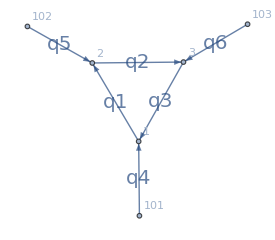

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[1,2,1],
DirectedEdge[2,3,2],
DirectedEdge[3,1,3],
DirectedEdge[101,1,4],
DirectedEdge[102,2,5],
DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|1->1,2->2,3->3|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1];
(*
Tri1Lnumerics={
k1->Evaluate[k1/.Tri1Lnumerics],
p1->Evaluate[p1/.Tri1Lnumerics],
p2->Evaluate[p2/.Tri1Lnumerics],
p3->Evaluate[p3/.Tri1Lnumerics],
p1E->0,
p2E->0,
p3E->0
}
*)
```

```mathematica
(
(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics]/.{λ->1})
-
(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[3],q[3]]-3^2),
"graph"->Tri1L,
"dots"-><|3->2|>
|>,
Tri1Lnumerics]/.{λ->1})
)
```

<|{-1,-1,1}→0,{-1,1,-1}→0,{-1,1,1}→0,{1,-1,-1}→0,{1,-1,1}→0,{1,1,-1}→0|>

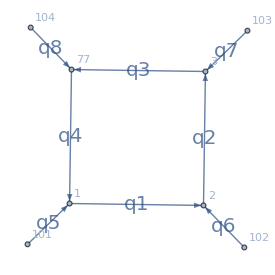

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],
DirectedEdge[2,3,2],
DirectedEdge[3,77,3],
DirectedEdge[77,1,4],
DirectedEdge[101,1,5],
DirectedEdge[102,2,6],
DirectedEdge[103,3,7],
DirectedEdge[104,77,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=AssignSignatures[Box1L,masses-><|1->1,2->2,3->3,4->3|>,lmb->{4}];
Box1L=DirectedGraph[Box1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Box1L]}]]
```

```mathematica
Dataset[Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Tri1L]}]]]
Dataset[Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Box1L]}]]]
```

```mathematica
Box1Lnumerics=Join[Tri1Lnumerics,{p4->{0,0,0},p4E->0}]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147,p4→{0,0,0},p4E→0}

```mathematica
{
Total[Values[(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True],Box1L],
"num"->1,
"graph"->Box1L,
"dots"-><||>
|>,
Box1Lnumerics]/.{λ->1})]]
,
Total[Values[(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><|3->2|>
|>,
Tri1Lnumerics]/.{λ->1})]]
}//N
(%⟦1⟧)/(%⟦2⟧)
```

{0.0000399946,-0.0000399946}

-1.